```mathematica
InNodes[g_,v_]:=Map[First,Select[EdgeList[g],(#[[2]] == v)&]]
```

```mathematica
OutNodes[g_,v_]:=Block[{out=VertexOutComponent[g,{v}]},Select[out,#≠v&]]
```

```mathematica
Select[VertexList[VertexOutComponent[g,v]],#≠v&]
```

```mathematica
MobiusMatrix[g_]:=Block[{vertices=VertexList[g], zero, result=Association[], todo,current, outNodes, out},
Table[result[v]=0,{v,vertices}];
zero=First[Select[vertices,VertexOutDegree[g,#]==0&]];
result[zero]=1;
todo=InNodes[g,zero];
While[todo≠{},
current=First[todo];
todo=Rest[todo];
out=OutNodes[g,current];
result[current]=-Total[Table[result[v],{v,out}]];
todo=Join[todo,InNodes[g,current]]
];
result
]
```

```mathematica
MobiusMatrix[gg]
```

<|{{1},{1},{1},{1},{1}}→0,{{5}}→1,{{2},{1},{1},{1}}→-1,{{2},{2},{1}}→1,{{3},{1},{1}}→1,{{3},{2}}→-1,{{4},{1}}→-1|>

```mathematica
ToLabels[assoc_]:=Table[key->Rotate[Column[{Row[key],Style[assoc[key],Bold,Red]}],Pi/6],{key,Keys[assoc]}]
```

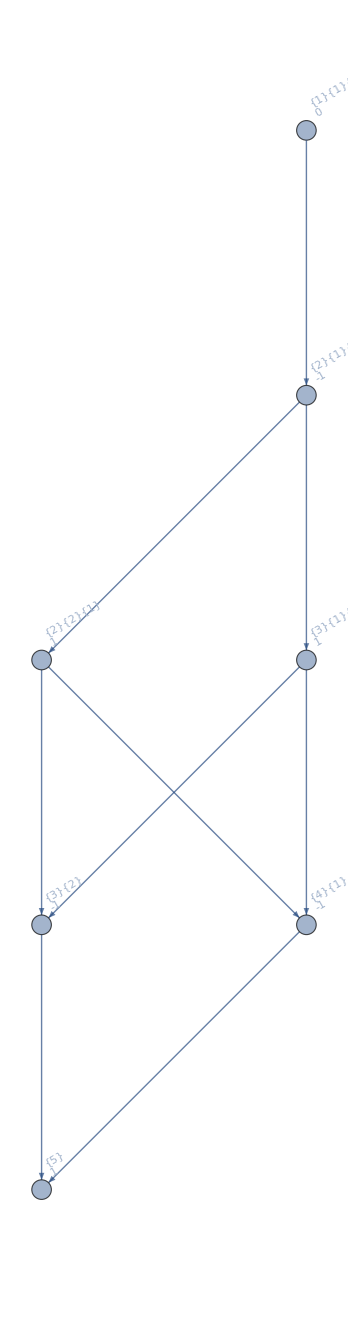

```mathematica
Graph[EdgeList[gg],VertexLabels->ToLabels[MobiusMatrix[gg]]]
```

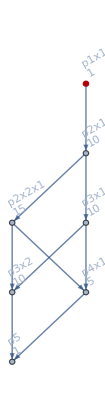
```mathematica
gg=-Graphics-;
```

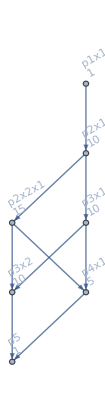

```mathematica
PartitionTypeLattice3[PartitionTypeFormula[allGraphs5[0,"graph"]]]
```

```mathematica
MobiusMatrix[%]
```

<|{{1},{1},{1},{1},{1}}→0,{{5}}→1,{{2},{1},{1},{1}}→-1,{{2},{2},{1}}→1,{{3},{1},{1}}→1,{{3},{2}}→-1,{{4},{1}}→-1|>

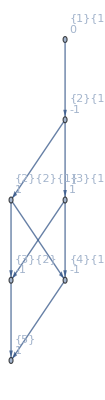

```mathematica
With[{ggg=PartitionTypeLattice3[PartitionTypeFormula[allGraphs5[0,"graph"]]]},
Graph[EdgeList[ggg],VertexLabels->ToLabels[MobiusMatrix[ggg]], GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
PartitionTypeLattice[IntegerPartitions[3]]
```

{{2,1}->{3},{1,1,1}->{2,1}}

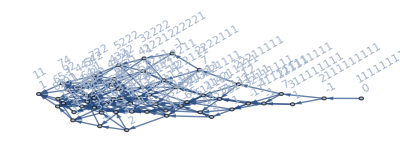

```mathematica
With[{ggg=PartitionTypeLattice[IntegerPartitions[11]]},
Graph[EdgeList[ggg],VertexLabels->ToLabels[MobiusMatrix[ggg]]]
]
```